```mathematica
ss[n_,s_]:=Tan[s Log[n]+ArcTan[1/(2 s)]]
```

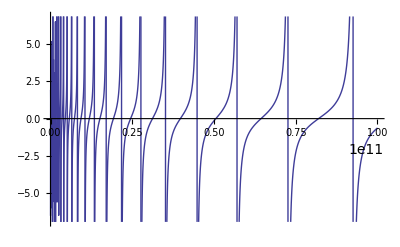

```mathematica
Plot[Re@ss[n,13],{n,0,100000000000}]
```

```mathematica
Limit[ ss[n,.01I+13],n->Infinity]
```

0.+1. ⅈ

```mathematica
tc[n_,s_]:=Sum[ j^(-1/2) Cos[s Log[j]],{j,1,n}]
tc2[n_,s_]:=Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]
tc3[n_,s_]:= tc[n,s]+ss[n,s]tc2[n,s]
tc4[n_,s_]:=Sum[ j^(-1/2) Cos[s Log[j]],{j,1,n}]+Tan[s Log[n]+ArcTan[1/(2 s)]]Sum[ j^(-1/2)Sin[s Log[j]],{j,1,n}]
```

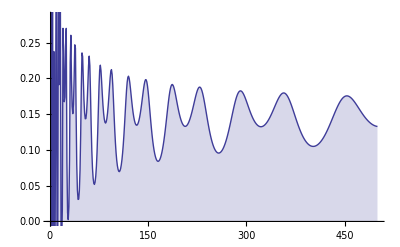

```mathematica
DiscretePlot[Re@tc3[n,N@Im@ZetaZero@1+.2I],{n,1,500}]
```

```mathematica
tc4[10000,.2I+5]
```

0.736957-0.21064 ⅈ

```mathematica
Zeta[.7+5I]
```

0.726329+0.209087 ⅈ

```mathematica
1/2+(.2I+5)I
```

0.3+5. ⅈ

```mathematica
((.7+5I)-1/2)/I
```

5.-0.2 ⅈ

```mathematica
sr[t_]:=1/2+t I
```

```mathematica
sr[.2I+5]
```

0.3+5. ⅈ

```mathematica
FullSimplify[(s+I/2)/I]
```

1/2-ⅈ s

```mathematica
1/2-(.7+5I)I
```

5.5-0.7 ⅈ

```mathematica
rr[n_,s_,t_]:= ((1-s)n^s HarmonicNumber[n,s]-(1-t)n^t HarmonicNumber[n,t])/((1-s)n^s -(1-t)n^t )
rr2[n_,s_,t_]:= ((1-s)n^s HarmonicNumber[n,s]-(1-t)n^t HarmonicNumber[n,t])/((1-s)n^s )
rr3[n_,s_,t_]:= HarmonicNumber[n,s]-(1-t)n^t/((1-s)n^s ) HarmonicNumber[n,t]
rr4a[n_,m_,d_]:= ((1-(m-d))n^(m-d) HarmonicNumber[n,(m-d)]-(1-(m+d))n^(m+d) HarmonicNumber[n,(m+d)])/((1-(m-d))n^(m-d) -(1-(m+d))n^(m+d) )
rr4[n_,s_,t_]:=rr4a[n,(s+t)/2,(s-t)/2]
rr5a[n_,m_,d_]:= ((1-m+d)E^((m-d)Log[n]) HarmonicNumber[n,m-d]-(1-m-d)E^((m+d)Log[n]) HarmonicNumber[n,m+d])/((1-m+d)E^((m-d)Log[n]) -(1-m-d)E^((m+d)Log[n]) )
rr5[n_,s_,t_]:=rr5a[n,(s+t)/2,(s-t)/2]
rr6a[n_,m_,d_]:= (((1-m+d)/(1-m-d))^(1/2)E^((m-d)Log[n]) HarmonicNumber[n,m-d]-((1-m+d)/(1-m-d))^(-1/2)E^((m+d)Log[n]) HarmonicNumber[n,m+d])/(((1-m+d)/(1-m-d))^(1/2)E^((m-d)Log[n]) -((1-m+d)/(1-m-d))^(-1/2)E^((m+d)Log[n]) )
rr6[n_,s_,t_]:=rr6a[n,(s+t)/2,(s-t)/2]
rr7a[n_,m_,d_]:= (E^Log[((1-m+d)/(1-m-d))^(1/2)]E^((m-d)Log[n]) HarmonicNumber[n,m-d]-E^Log[((1-m+d)/(1-m-d))^(-1/2)]E^((m+d)Log[n]) HarmonicNumber[n,m+d])/(E^Log[((1-m+d)/(1-m-d))^(1/2)]E^((m-d)Log[n]) -E^Log[((1-m+d)/(1-m-d))^(-1/2)]E^((m+d)Log[n]) )
rr7[n_,s_,t_]:=rr7a[n,(s+t)/2,(s-t)/2]
rr8a[n_,m_,d_]:= (E^ArcTanh[d/(1-m)]E^((m-d)Log[n]) HarmonicNumber[n,m-d]-E^-ArcTanh[d/(1-m)]E^((m+d)Log[n]) HarmonicNumber[n,m+d])/(E^ArcTanh[d/(1-m)]E^((m-d)Log[n]) -E^-ArcTanh[d/(1-m)]E^((m+d)Log[n]) )
rr8[n_,s_,t_]:=rr8a[n,(s+t)/2,(s-t)/2]
rr9a[n_,m_,d_]:= (E^((m-d)Log[n]+ArcTanh[d/(1-m)]) HarmonicNumber[n,m-d]-E^((m+d)Log[n]-ArcTanh[d/(1-m)]) HarmonicNumber[n,m+d])/(E^((m-d)Log[n]+ArcTanh[d/(1-m)]) -E^((m+d)Log[n]-ArcTanh[d/(1-m)]) )
rr9[n_,s_,t_]:=rr9a[n,(s+t)/2,(s-t)/2]
rr10a[n_,m_,d_]:= Sum[ (E^((m-d)Log[n/j]+ArcTanh[d/(1-m)]) -E^((m+d)Log[n/j]-ArcTanh[d/(1-m)]) )/(E^((m-d)Log[n]+ArcTanh[d/(1-m)]) -E^((m+d)Log[n]-ArcTanh[d/(1-m)]) ),{j,1,n}]
rr10[n_,s_,t_]:=rr9a[n,(s+t)/2,(s-t)/2]
rr11a[n_,m_,d_]:=Sum[j^-m  Sinh[ArcTanh[d/(-1+m)]+d Log[n/j]]/Sinh[ArcTanh[d/(-1+m)]+d Log[n]],{j,1,n}]
rr11[n_,s_,t_]:=rr11a[n,(s+t)/2,(s-t)/2]
rr12a[n_,m_,d_]:=Sum[j^-m  (Sinh[ArcTanh[d/(-1+m)]+d Log[n]]Cosh[d Log[j]]-Cosh[ArcTanh[d/(-1+m)]+d Log[n]]Sinh[d Log[j]])/Sinh[ArcTanh[d/(-1+m)]+d Log[n]],{j,1,n}]
rr12[n_,s_,t_]:=rr12a[n,(s+t)/2,(s-t)/2]
rr13a[n_,m_,d_]:=(1/Sinh[ArcTanh[d/(-1+m)]+d Log[n]])(Sinh[ArcTanh[d/(-1+m)]+d Log[n]]Sum[j^-m  Cosh[d Log[j]],{j,1,n}]-Cosh[ArcTanh[d/(-1+m)]+d Log[n]]Sum[j^-m  Sinh[d Log[j]],{j,1,n}])
rr13[n_,s_,t_]:=rr13a[n,(s+t)/2,(s-t)/2]
rr14a[n_,m_,d_]:=Sum[j^-m  Cosh[d Log[j]],{j,1,n}]-Coth[ArcTanh[d/(-1+m)]+d Log[n]]Sum[j^-m  Sinh[d Log[j]],{j,1,n}]
rr14[n_,s_,t_]:=rr14a[n,(s+t)/2,(s-t)/2]
```

```mathematica
rr14[100000,.2+6I,.2-6I]
```

0.820972+0. ⅈ

```mathematica
rr14[n,s+t I,s - t I]
```

∑_(j=1)^n j^-s Cos[t Log[j]]+ⅈ Cot[ArcTan[t/(-1+s)]+t Log[n]] ∑_(j=1)^n ⅈ j^-s Sin[t Log[j]]

```mathematica
Log[((1+d-m)/(1-m-d))^(1/2)]/.m->.4/.d->.2
```

0.346574

```mathematica
ArcTanh[d/(1-m)]/.m->.4/.d->.2
```

0.346574

```mathematica
(1/2)Log[((1+d-m)/(1-m-d))]/.m->.4/.d->.2
```

0.346574

```mathematica
(1/2)(Log[((1-m)+d)]-Log[(1-m)-d])/.m->.4/.d->.2
```

0.346574

```mathematica
(1/2)(Log[(1+d/(1-m))]-Log[1-d/(1-m)])/.m->.4/.d->.2
```

0.346574

```mathematica
ExpToTrig[(E^((m-d)Log[n/j]+ArcTanh[d/(1-m)]) -E^((m+d)Log[n/j]-ArcTanh[d/(1-m)]) )/(E^((m-d)Log[n]+ArcTanh[d/(1-m)]) -E^((m+d)Log[n]-ArcTanh[d/(1-m)])) ]
```

(Cosh[ArcTanh[d/(1-m)]+(-d+m) Log[n/j]]-Cosh[ArcTanh[d/(1-m)]-(d+m) Log[n/j]]+Sinh[ArcTanh[d/(1-m)]+(-d+m) Log[n/j]]+Sinh[ArcTanh[d/(1-m)]-(d+m) Log[n/j]])/(Cosh[ArcTanh[d/(1-m)]+(-d+m) Log[n]]-Cosh[ArcTanh[d/(1-m)]-(d+m) Log[n]]+Sinh[ArcTanh[d/(1-m)]+(-d+m) Log[n]]+Sinh[ArcTanh[d/(1-m)]-(d+m) Log[n]])

```mathematica
FullSimplify[(Cosh[ArcTanh[d/(1-m)]+(-d+m) Log[n/j]]-Cosh[ArcTanh[d/(1-m)]-(d+m) Log[n/j]]+Sinh[ArcTanh[d/(1-m)]+(-d+m) Log[n/j]]+Sinh[ArcTanh[d/(1-m)]-(d+m) Log[n/j]])/(Cosh[ArcTanh[d/(1-m)]+(-d+m) Log[n]]-Cosh[ArcTanh[d/(1-m)]-(d+m) Log[n]]+Sinh[ArcTanh[d/(1-m)]+(-d+m) Log[n]]+Sinh[ArcTanh[d/(1-m)]-(d+m) Log[n]])]
```

n^-m (n/j)^m Csch[ArcTanh[d/(-1+m)]+d Log[n]] Sinh[ArcTanh[d/(-1+m)]+d Log[n/j]]

```mathematica
Cosh[ArcTanh[d/(-1+m)]+d Log[n]]/Sinh[ArcTanh[d/(-1+m)]+d Log[n]]
```

Coth[ArcTanh[d/(-1+m)]+d Log[n]]

```mathematica
Sum[j^-m  Cosh[d Log[j]],{j,1,n}]-Coth[ArcCoth[(m-1)/d]+d Log[n]]Sum[j^-m  Sinh[d Log[j]],{j,1,n}]/.m->0
```

∑_(j=1)^n Cosh[d Log[j]]+Coth[ArcCoth[1/d]-d Log[n]] ∑_(j=1)^n Sinh[d Log[j]]

```mathematica
ArcTanh[d/(m-1)]/.m->.4/.d->.3
```

-0.549306

```mathematica
ArcCoth[(m-1)/d]/.m->.4/.d->.3
```

-0.549306

```mathematica
Limit[Tanh[0 Log[n]],n->Infinity]
```

0

```mathematica
FullSimplify[∑_(j=1)^n j^-s Cos[t Log[j]]+ⅈ Cot[ArcTan[t/(-1+s)]+t Log[n]] ∑_(j=1)^n ⅈ j^-s Sin[t Log[j]]]
```

∑_(j=1)^n j^-s Cos[t Log[j]]+ⅈ Cot[ArcTan[t/(-1+s)]+t Log[n]] ∑_(j=1)^n ⅈ j^-s Sin[t Log[j]]

```mathematica
ax[n_,s_,t_]:=∑_(j=1)^n j^-s Cos[t Log[j]]+ⅈ Cot[ArcTan[t/(-1+s)]+t Log[n]] ∑_(j=1)^n ⅈ j^-s Sin[t Log[j]]
ax2[n_,s_,t_]:=∑_(j=1)^n N[j^-s Cos[t Log[j]]]- Cot[ArcTan[t/(-1+s)]+t Log[n]] ∑_(j=1)^n N[j^-s Sin[t Log[j]]]
ax3[n_,s_,t_]:=((1-s+ⅈ t) HarmonicNumber[n,s-ⅈ t]+n^(2 ⅈ t) (-1+s+ⅈ t) HarmonicNumber[n,s+ⅈ t])/(1-s+n^(2 ⅈ t) (-1+s+ⅈ t)+ⅈ t)
```

```mathematica
ax3[1000000000000,.5,N@Im@ZetaZero@1+3]
```

3.04084+3.67284×10^-12 ⅈ

```mathematica
Zeta[N@ZetaZero@1+3I]
```

2.053+0.7817 ⅈ

```mathematica
TrigToExp[∑_(j=1)^n j^-s Cos[t Log[j]]+ⅈ Cot[ArcTan[t/(-1+s)]+t Log[n]] ∑_(j=1)^n ⅈ j^-s Sin[t Log[j]]]
```

```mathematica
FullSimplify[Sum[(1/2 j^(-s-ⅈ t)+1/2 j^(-s+ⅈ t)),{j,1,n}]+((ⅇ^(1/2 (Log[1-(ⅈ t)/(-1+s)]-Log[1+(ⅈ t)/(-1+s)])) n^(-ⅈ t)+ⅇ^(1/2 (-Log[1-(ⅈ t)/(-1+s)]+Log[1+(ⅈ t)/(-1+s)])) n^(ⅈ t)) ∑_(j=1)^n (-1/2 j^(-s-ⅈ t)+1/2 j^(-s+ⅈ t)))/(ⅇ^(1/2 (Log[1-(ⅈ t)/(-1+s)]-Log[1+(ⅈ t)/(-1+s)])) n^(-ⅈ t)-ⅇ^(1/2 (-Log[1-(ⅈ t)/(-1+s)]+Log[1+(ⅈ t)/(-1+s)])) n^(ⅈ t))]
```

((1-s+ⅈ t) HarmonicNumber[n,s-ⅈ t]+n^(2 ⅈ t) (-1+s+ⅈ t) HarmonicNumber[n,s+ⅈ t])/(1-s+n^(2 ⅈ t) (-1+s+ⅈ t)+ⅈ t)

```mathematica
rr14a[n_,m_,d_]:=Sum[j^-m  Cosh[d Log[j]],{j,1,n}]-Coth[ArcTanh[d/(-1+m)]+d Log[n]]Sum[j^-m  Sinh[d Log[j]],{j,1,n}]
rr14a2[n_,m_,d_]:={Sum[j^-m  Cosh[d Log[j]],{j,1,n}],-Coth[ArcTanh[d/(-1+m)]+d Log[n]],Sum[j^-m  Sinh[d Log[j]],{j,1,n}]}
rr14[n_,s_,t_]:=rr14a[n,(s+t)/2,(s-t)/2]
```

```mathematica
rr14a2[1000.,0,N@ZetaZero@1+.4]
```

{-6696.21+16263.8 ⅈ,-0.999994-4.80011×10^-6 ⅈ,-6696.44+16263.9 ⅈ}

```mathematica
rr14a[n,0,s]
```

∑_(j=1)^n Cosh[s Log[j]]+Coth[ArcTanh[s]-s Log[n]] ∑_(j=1)^n Sinh[s Log[j]]

```mathematica
so[n_,s_]:=∑_(j=1)^n Cosh[s Log[j]]+Coth[ArcTanh[s]-s Log[n]] ∑_(j=1)^n Sinh[s Log[j]]
so2[n_,s_]:=∑_(j=1)^n (j^-s/2+j^s/2+(ⅇ^(1/2 (-Log[1-s]+Log[1+s])) n^-s+ⅇ^(1/2 (Log[1-s]-Log[1+s])) n^s)/(ⅇ^(1/2 (-Log[1-s]+Log[1+s])) n^-s-ⅇ^(1/2 (Log[1-s]-Log[1+s])) n^s)(-j^-s/2+j^s/2))
so3[n_,s_]:=∑_(j=1)^n ((j^-s (n^(2 s) (-1+s)+j^(2 s) (1+s)))/(1+n^(2 s) (-1+s)+s))
```

```mathematica
FullSimplify[so3[n,s]/so3[n,1-s]]
```

((n^(2 s) (-2+s)+n^2 s) ((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s]+n^(2 s) (-2+s) HarmonicNumber[n,-1+s]))

```mathematica
FullSimplify[so3[n,s]/so3[n,1-s/2]]
```

((n^s (-4+s)+n^2 s) ((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s/2]+n^s (-4+s) HarmonicNumber[n,-1+s/2]))

```mathematica
rr14b[n_,s_]:=∑_(j=1)^n Cosh[s Log[j]]+Coth[ArcTanh[s]-s Log[n]] ∑_(j=1)^n Sinh[s Log[j]]
rr14c[n_,s_]:=∑_(j=1)^n (j^-s/2+j^s/2)+Coth[ArcTanh[s]-s Log[n]] ∑_(j=1)^n (-j^-s/2+j^s/2)
rr14d[n_,s_]:=∑_(j=1)^n (j^-s/2+j^s/2)+(-1+(2 (1+s))/(1+n^(2 s) (-1+s)+s)) ∑_(j=1)^n (-j^-s/2+j^s/2)
rr14d2[n_,s_]:=∑_(j=1)^n (j^-s/2+j^s/2)+(-1+2/(1+n^(2 s) (-1+s)/(1+s))) ∑_(j=1)^n (-j^-s/2+j^s/2)
rr14e[n_,s_]:=((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s])/(1+n^(2 s) (-1+s)+s)
rr14f[n_,s_]:=((1+s) HarmonicNumber[n,-s])/((s+1)+n^(2 s) (-1+s))+(n^(2 s) (-1+s) HarmonicNumber[n,s])/((s+1)+n^(2 s) (-1+s))
rr14g[n_,s_]:=HarmonicNumber[n,-s]/(1+n^(2 s) (-1+s)/(s+1))+HarmonicNumber[n,s]/(n^(-2s)(s+1)/(s-1)+ 1)
rr14ga[n_,s_]:={HarmonicNumber[n,-s]/(1+n^(2 s) (s-1)/(s+1)),HarmonicNumber[n,s]/(n^(-2s)(s+1)/(s-1)+ 1)}
```

```mathematica
TrigToExp[Sinh[s Log[j]]]
```

-j^-s/2+j^s/2

```mathematica
rr14d2[100000,.3]
```

-0.919274

```mathematica
Zeta[.3]
```

-0.904559

```mathematica
FullSimplify[TrigToExp[Coth[ArcTanh[s]-s Log[n]]]]
```

-1+(2 (1+s))/(1+n^(2 s) (-1+s)+s)

```mathematica
FullSimplify[∑_(j=1)^n (j^-s/2+j^s/2)+(-1+(2 (1+s))/(1+n^(2 s) (-1+s)+s)) ∑_(j=1)^n (-j^-s/2+j^s/2)]
```

((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s])/(1+n^(2 s) (-1+s)+s)

```mathematica
FullSimplify[((1+s) HarmonicNumber[n,-s])/((s+1)+n^(2 s) (-1+s))]
```

((1+s) HarmonicNumber[n,-s])/(1+n^(2 s) (-1+s)+s)

```mathematica
FullSimplify[(n^(2 s) (-1+s) HarmonicNumber[n,s])/((s+1)+n^(2 s) (-1+s))]
```

(n^(2 s) (-1+s) HarmonicNumber[n,s])/(1+n^(2 s) (-1+s)+s)

```mathematica
rr14a[n_,m_,d_]:=Sum[j^-m  Cosh[d Log[j]],{j,1,n}]-Coth[ArcTanh[d/(-1+m)]+d Log[n]]Sum[j^-m  Sinh[d Log[j]],{j,1,n}]
```

```mathematica
rr14a[n,s,t]
```

∑_(j=1)^n j^-s Cosh[t Log[j]]-Coth[ArcTanh[t/(-1+s)]+t Log[n]] ∑_(j=1)^n j^-s Sinh[t Log[j]]

```mathematica
pl[n_,s_,t_]:=(∑_(j=1)^n j^-s Cosh[t Log[j]])/( ∑_(j=1)^n j^-s Sinh[t Log[j]])
```

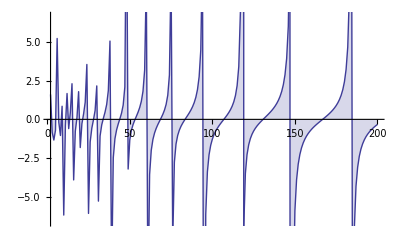

```mathematica
DiscretePlot[ Im@pl[n,.6,N@ZetaZero@1-1/2],{n,2,200}]
```

```mathematica
pl[100,.5,N@ZetaZero@1-1/2]
```

0.-0.978974 ⅈ

```mathematica
rr14g[n_,s_]:=HarmonicNumber[n,-s]/(1+n^(2 s) (-1+s)/(s+1))+HarmonicNumber[n,s]/(n^(-2s)(s+1)/(s-1)+ 1)
rr14gx[n_,s_]:={1/(1+n^(2 s) (-1+s)/(s+1)),HarmonicNumber[n,-s],1/(n^(-2s)(s+1)/(s-1)+ 1),HarmonicNumber[n,s]}
```

```mathematica
FullSimplify[rr14g[n,s]/rr14g[n ,1-s]]
```

((n^(2 s) (-2+s)+n^2 s) ((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s]+n^(2 s) (-2+s) HarmonicNumber[n,-1+s]))

```mathematica
fa[s_]:=2^s Pi^(s-1)Sin[ Pi s/ 2] Gamma[ 1-s]
fb[n_,s_]:=((n^(2 s) (-2+s)+n^2 s) ((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s]+n^(2 s) (-2+s) HarmonicNumber[n,-1+s]))
fc[n_,s_]:=((n^(2 s) (-2+s)+n^2 s) (1+s) HarmonicNumber[n,-s])/((1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s]+n^(2 s) (-2+s) HarmonicNumber[n,-1+s]))+((n^(2 s) (-2+s)+n^2 s) n^(2 s) (-1+s) HarmonicNumber[n,s])/((1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s]+n^(2 s) (-2+s) HarmonicNumber[n,-1+s]))
```

```mathematica
fc[10000,.3]
```

0.33656

```mathematica
fb[10000,.3]
```

0.33656

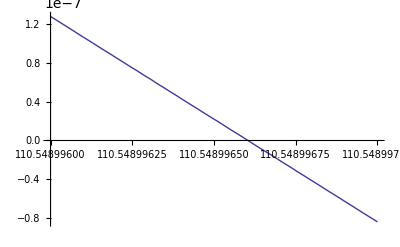

```mathematica
Plot[ Re@Zeta[.8+s I],{s,110.548996,110.548997}]
```

```mathematica
Zeta[.8+110.548996I]
```

1.27293×10^-7-0.929295 ⅈ

```mathematica
ps[n_,s_]:= Re[(1-Tanh[ArcTanh[1/(2s)]-s Log[n]])HarmonicNumber[n,1/2+s]]
psf[n_,s_]:= Re[(1-Tanh[ArcTanh[1/(2s-1)]-(s-1/2) Log[n]])HarmonicNumber[n,s]]
psx[n_,s_]:= (1-Tanh[ArcTanh[1/(2s)]-s Log[n]])HarmonicNumber[n,1/2+s]
psx2[n_,s_]:= ((1-Tanh[ArcTanh[1/(2s)]-s Log[n]])HarmonicNumber[n,1/2+s]+(1+Tanh[ArcTanh[1/(2s)]-s Log[n]])HarmonicNumber[n,1/2-s])/2
psx2a[n_,s_]:= {(1-Tanh[ArcTanh[1/(2s)]-s Log[n]])HarmonicNumber[n,1/2+s]/2,(1+Tanh[ArcTanh[1/(2s)]-s Log[n]])HarmonicNumber[n,1/2-s]/2}
```

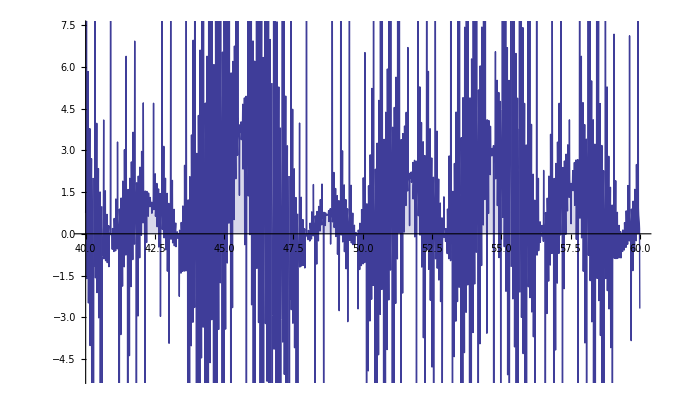

```mathematica
DiscretePlot[psf[10000000000000000000000,.5+s I],{s,40,60,.01}]
```

```mathematica
psx2[10000000000,.8+110.548996I-1/2]
```

1.3437×10^-6-0.929293 ⅈ

```mathematica
psx3[n_,s_]:= ((1-Tanh[ArcTanh[1/(2s)]-s Log[n]])HarmonicNumber[n,1/2+s]+(1+Tanh[ArcTanh[1/(2s)]-s Log[n]])HarmonicNumber[n,1/2-s])/2
f2[n_,s_]:=  (1+Tanh[ArcTanh[1/(1-2s)]+(s-1/2) Log[n]])/2 HarmonicNumber[n,s]
f3[n_,s_]:=(1-n^(1-2 s) s/(1-s))^-1HarmonicNumber[n,s]
f3a[n_,s_]:={(1-n^(1-2 s) s/(1-s))^-1,HarmonicNumber[n,s]}
psx4[n_,s_]:=f2[n,s]+f2[n,1-s]
psx5[n_,s_]:=f3[n,s]+f3[n,1-s]
```

```mathematica
psx3[n,1/2-s]
```

1/2 (HarmonicNumber[n,1-s] (1-Tanh[ArcTanh[1/(2 (1/2-s))]-(1/2-s) Log[n]])+HarmonicNumber[n,s] (1+Tanh[ArcTanh[1/(2 (1/2-s))]-(1/2-s) Log[n]]))

```mathematica
f2[n,1-s]
```

1/2 HarmonicNumber[n,1-s] (1+Tanh[ArcTanh[1/(1-2 (1-s))]+(1/2-s) Log[n]])

```mathematica
f3a[10000000000000,N@ZetaZero@1]
```

{0.5-0.739634 ⅈ,185231.-125218. ⅈ}

```mathematica
psx5[100000000000,N@ZetaZero@1+2I]
```

0.710167+0. ⅈ

```mathematica
Zeta[.8+12I]
```

0.987421-0.602699 ⅈ

```mathematica
FullSimplify[TrigToExp[(1+Tanh[ArcTanh[1/(1-2s)]+(s-1/2) Log[n]])/2]]
```

1/(1+(n^(1-2 s) s)/(-1+s))

```mathematica
((1-s)n^s)/((1-s)n^s-n^(1- s) s)
```

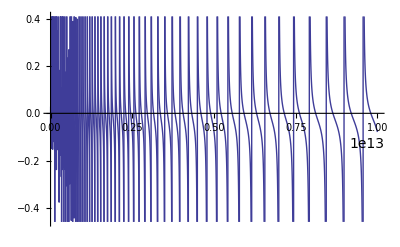

```mathematica
Plot[Re[f3[n,N@ZetaZero@10+.1I]],{n,1,10000000000000}]
```

```mathematica
al[s_]:=1/(1/2 Pi^(-s/2)Gamma[s/2]s(s+1))
al2[s_]:=(1/2)s(s-1)Pi^(-s/2)Gamma[1/2s]
f4[n_,s_]:=(al[s]-al[1-s]n^(1-2s)s/(1-s))^-1 HarmonicNumber[n,s]
xi[n_,s_]:=f4[n,s]+f4[n,1-s]
zt[n_,s_]:=al[s]xi[n,s]
```

```mathematica
zt[10000000000000000,.6+7I]
```

1.02336+0.376035 ⅈ

```mathematica
Zeta[.6+7I]
```

1.02297+0.375953 ⅈ

```mathematica
xi[100000000000000,.6+7I]
```

0.151263-0.0378792 ⅈ

```mathematica
Zeta[.6+7I]al2[.6+7I]
```

0.152156+0.00540746 ⅈ

```mathematica
f4[10000000000,N@ZetaZero@2]
```

-2.73865×10^-10-0.260547 ⅈ

```mathematica
f6[n_,s_]:=(1-n^(1-2 s) s/(1-s))^-1HarmonicNumber[n,s]
f6a[n_,s_]:=n^(s-1/2) (1-s)HarmonicNumber[n,s]
f6b[n_,s_]:=n^(s-3/5) (1-s)HarmonicNumber[n,s]
```

```mathematica
f6b[1000000000000000000000,N@ZetaZero@300]
```

2.51189×10^8+7.45058×10^-9 ⅈ

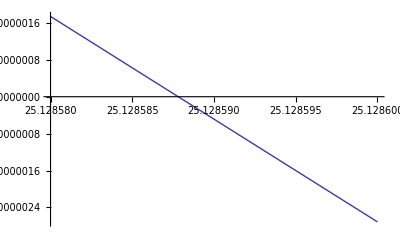

```mathematica
Plot[ Re@Zeta[.53+s I],{s,25.12858,25.1286}]
```

```mathematica
Zeta[.53+25.12858 I]
```

1.73886×10^-6+0.165551 ⅈ

```mathematica
f6[1000000000,.53+25.12858 I]
```

-285.103+565.901 ⅈ

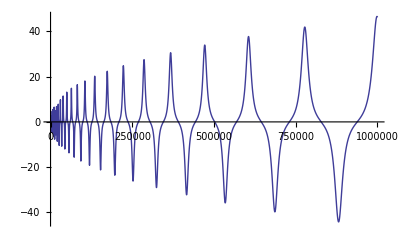

```mathematica
Plot[ Re@f6[n,.53+25.12858 I],{n,1,1000000}]
```

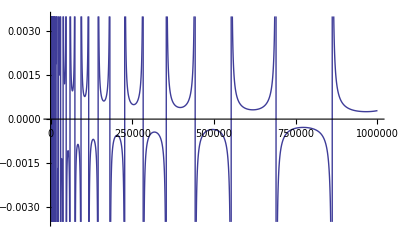

```mathematica
Plot[ Re@f6[n,N@ZetaZero@1],{n,1,1000000}]
```

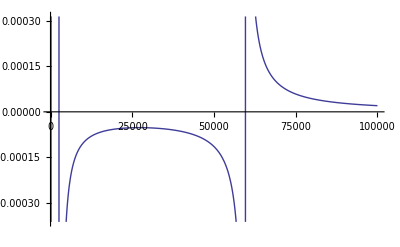

```mathematica
Plot[1/(x  Cos[Log@x] ),{x,1,100000}]
```

```mathematica
Limit[ 1/(x Cos[Log[x]]),x->Infinity]
```

Limit[Sec[Log[x]]/x,x→∞]

```mathematica
rr14g[n_,s_]:=HarmonicNumber[n,-s]/(1+n^(2 s) (-1+s)/(s+1))+HarmonicNumber[n,s]/(n^(-2s)(s+1)/(s-1)+ 1)
rr14gx[n_,s_]:={1/(1+n^(2 s) (-1+s)/(s+1)),HarmonicNumber[n,-s],1/(n^(-2s)(s+1)/(s-1)+ 1),HarmonicNumber[n,s]}
```

```mathematica
FullSimplify[rr14g[n,s]/rr14g[n ,1-s]]
```

((n^(2 s) (-2+s)+n^2 s) ((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s]+n^(2 s) (-2+s) HarmonicNumber[n,-1+s]))

```mathematica
fa[s_]:=2^s Pi^(s-1)Sin[ Pi s/ 2] Gamma[ 1-s]
fas[s_]:=1/2 s(s-1)Pi^(-s/2)Gamma[s/2]
fax[s_]:=fas[1-s]/fas[s]
fba[n_,s_]:=((n^(2 s)(s-2) +n^2 s) ((s+1) HarmonicNumber[n,-s]+n^(2 s) (s-1) HarmonicNumber[n,s]))/(((s+1)+n^(2 s) (s-1)) (n^2 s HarmonicNumber[n,1-s]+n^(2 s) (s-2) HarmonicNumber[n,s-1]))
fba2[n_,s_]:=((n^(2 s)(s-2) +n^2 s)Sum[ ((s+1) j^s+n^(2 s) (s-1) j^-s),{j,1,n}])/(((s+1)+n^(2 s) (s-1)) Sum[(n^2 s j^-(1-s)+n^(2 s) (s-2) j^-(s-1)),{j,1,n}])
fba3[n_,s_]:=((n^(s-1)(s-2) +n^(1-s) s)Sum[ (n^(-s-1)(s+1) j^s+n^(s-1) (s-1) j^-s),{j,1,n}])/((n^(-s-1)(s+1)+n^(s-1) (s-1)) Sum[(n^(1-s) s j^-(1-s)+n^(s-1) (s-2) j^-(s-1)),{j,1,n}])
fbb[n_,s_]:=((n^(2 s)(s-2) +n^2 s) HarmonicNumber[n,0-s])/((1+n^(2 s) (s-1)/(s+1)) (n^2 s HarmonicNumber[n,1-s]+n^(2 s) (s-2) HarmonicNumber[n,s-1]))+((n^(2 s)(s-2) +n^2 s) ( HarmonicNumber[n,s-0]))/((1+(s+1)/(s-1)n^(-2 s)) (n^2 s HarmonicNumber[n,1-s]+n^(2 s) (s-2) HarmonicNumber[n,s-1]))
fbc[n_,s_]:=((n^(s-1)(s-2) +n^(1-s) s) HarmonicNumber[n,0-s])/((1+n^(2 s) (s-1)/(s+1)) (n^(1-s) s HarmonicNumber[n,1-s]+n^(s-1) (s-2) HarmonicNumber[n,s-1]))+((n^(s-1)(s-2) +n^(1-s) s) ( HarmonicNumber[n,s-0]))/((1+(s+1)/(s-1)n^(-2 s)) (n^(1-s) s HarmonicNumber[n,1-s]+n^(s-1) (s-2) HarmonicNumber[n,s-1]))
fbd[n_,s_]:=(n^(s-1)(s-2) +n^(1-s) s)(HarmonicNumber[n,-s]/((1+n^(2 s) (s-1)/(s+1)) (n^(1-s) s HarmonicNumber[n,1-s]+n^(s-1) (s-2) HarmonicNumber[n,s-1]))+HarmonicNumber[n,s]/((1+(s+1)/(s-1)n^(-2 s)) (n^(1-s) s HarmonicNumber[n,1-s]+n^(s-1) (s-2) HarmonicNumber[n,s-1])))
```

```mathematica
fa[.3+I]
```

-0.610073-0.275269 ⅈ

```mathematica
fax[.3+I]
```

-0.610073-0.275269 ⅈ

```mathematica
fba[100000000000,.3+I]
```

-0.610409-0.275615 ⅈ

```mathematica
fba3[10,.5+3I]
```

0.719881-0.694098 ⅈ

```mathematica
FullSimplify[(n^(s-1)(s-2) +n^(1-s) s)/(n^(-s-1)(s+1)+n^(s-1) (s-1))]
```

(n^(2 s) (-2+s)+n^2 s)/(1+n^(2 s) (-1+s)+s)

```mathematica
FullSimplify[rr14g[n,s]/rr14g[n ,1-s/2]]
```

((n^s (-4+s)+n^2 s) ((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s/2]+n^s (-4+s) HarmonicNumber[n,-1+s/2]))

```mathematica
ab[n_,s_]:=((n^s (-4+s)+n^2 s) ((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s/2]+n^s (-4+s) HarmonicNumber[n,-1+s/2]))
```

```mathematica
ab[1000000000000000000000,.9+2I]
```

-0.274712-0.813137 ⅈ

```mathematica
fas[1-s/2]/fas[s]/.s->.9+2I
```

-0.327492-0.856247 ⅈ

```mathematica
FullSimplify[rr14g[n,s]/rr14g[n ,1-s/3]]
```

((n^(2 s/3) (-6+s)+n^2 s) ((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s/3]+n^(2 s/3) (-6+s) HarmonicNumber[n,-1+s/3]))

```mathematica
ac[n_,s_]:=((n^(2 s/3) (-6+s)+n^2 s) ((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))/((1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s/3]+n^(2 s/3) (-6+s) HarmonicNumber[n,-1+s/3]))
```

```mathematica
ac[10000000000,.2+12I]
```

1.70478-1.21934 ⅈ

```mathematica
fas[1-s/3]/fas[s]/.s->.2+12I
```

72.7714-33.6692 ⅈ

```mathematica
fa[s_]:=2^s Pi^(s-1)Sin[ Pi s/ 2] Gamma[ 1-s]
fa2[s_]:=2^(1-s) π^-s Sin[1/2 π (1-s)] Gamma[s]
fba[n_,s_]:=((n^(2 s)(s-2) +n^2 s) ((s+1) HarmonicNumber[n,-s]+n^(2 s) (s-1) HarmonicNumber[n,s]))/(((s+1)+n^(2 s) (s-1)) (n^2 s HarmonicNumber[n,1-s]+n^(2 s) (s-2) HarmonicNumber[n,s-1]))
ffba[n_,s_]:=((n^(2 (1-s)) (-1-s)+n^2 (1-s)) (-n^(2 (1-s)) s HarmonicNumber[n,1-s]+(2-s) HarmonicNumber[n,-1+s]))/((2-s-n^(2 (1-s)) s) (n^(2 (1-s)) (-1-s) HarmonicNumber[n,-s]+n^2 (1-s) HarmonicNumber[n,s]))
fa3[s_]:= Gamma[s]
ffbb[n_,s_]:=((n^(2 (1-s)) (-1-s)+n^2 (1-s)) (-n^(2 (1-s)) s HarmonicNumber[n,1-s]+(2-s) HarmonicNumber[n,-1+s]))/(2^(1-s) π^-s Sin[1/2 π (1-s)](2-s-n^(2 (1-s)) s) (n^(2 (1-s)) (-1-s) HarmonicNumber[n,-s]+n^2 (1-s) HarmonicNumber[n,s]))
```

```mathematica
fa3[.3]
```

2.99157

```mathematica
ffbb[100000000,.3]
```

2.98588

```mathematica
FullSimplify[((n^(2 (1-s)) (-1-s)+n^2 (1-s)) (-n^(2 (1-s)) s HarmonicNumber[n,1-s]+(2-s) HarmonicNumber[n,-1+s]))/(2^(1-s) π^-s Sin[1/2 π (1-s)](2-s-n^(2 (1-s)) s) (n^(2 (1-s)) (-1-s) HarmonicNumber[n,-s]+n^2 (1-s) HarmonicNumber[n,s]))]
```

```mathematica
(2^(-1+s) π^s (1+n^(2 s) (-1+s)+s) (n^2 s HarmonicNumber[n,1-s]+n^(2 s) (-2+s) HarmonicNumber[n,-1+s]) Sec[(π s)/2])/((n^(2 s) (-2+s)+n^2 s) ((1+s) HarmonicNumber[n,-s]+n^(2 s) (-1+s) HarmonicNumber[n,s]))
```

```mathematica
f6[n_,s_]:=(1-n^(1-2 s) s/(1-s))^-1HarmonicNumber[n,s]
f6a[n_,s_]:=(1-n^(1-2 s) s/(1-s))^-1
```

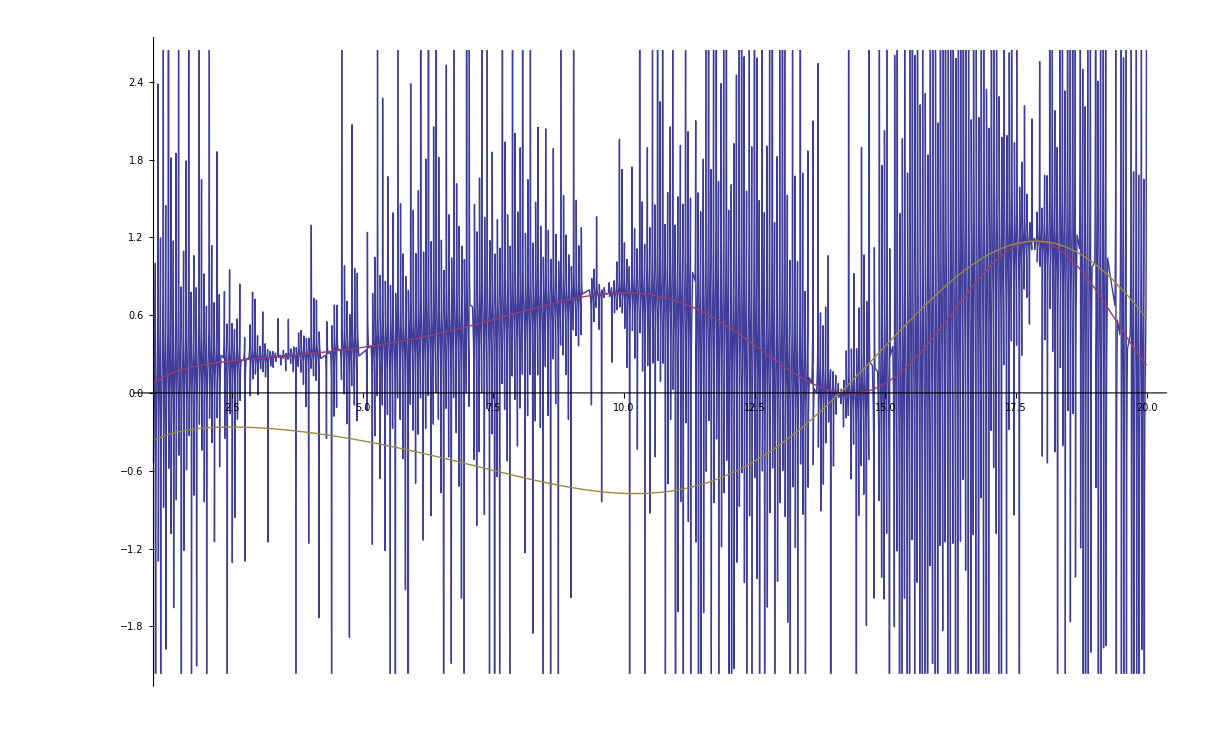

```mathematica
Plot[{Re@f6[10000000000000000000000000000,.5+s I],Re@Zeta[.5 + s I]/2,  RiemannSiegelZ[s]/2},{s,1,20}]
```

```mathematica
f6[10000000000000000000,.5+17.8455995404 I]
```

1.17009-1.24053×10^9 ⅈ

```mathematica
Zeta[.5+17.8455995404 I]/2
```

1.17009+6.63112×10^-12 ⅈ

```mathematica
f6[10000000000000000000,1-(.5+17.8455995404 I)]
```

1.17009+1.24053×10^9 ⅈ

```mathematica
f6[n,.5+17.8455995404 I]
```

HarmonicNumber[n,0.5+17.8456 ⅈ]/(1+(0.998431-0.0559923 ⅈ) n^(0.-35.6912 ⅈ))

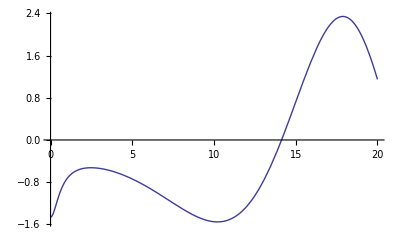

```mathematica
Plot[  RiemannSiegelZ[t],{t,0,20}]
```

```mathematica
RiemannSiegelTheta[27.6701822178]
```

6.28319

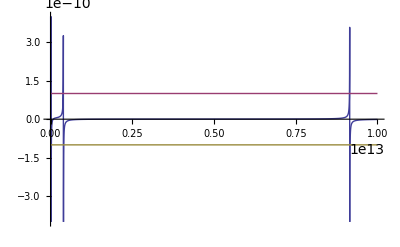

```mathematica
Plot[{ Tan[Log@x]/x,.0000000001,-.0000000001},{x,1000000,10000000000000}]
```

```mathematica
D[Sec[x]/x,x]
```

-Sec[x]/x^2+(Sec[x] Tan[x])/x

```mathematica
Limit[-Sec[x]/x^2+(Sec[x] Tan[x])/x,x->Infinity]
```

Limit[-Sec[x]/x^2+(Sec[x] Tan[x])/x,x→∞]

```mathematica
Clear[tsa]
ts[n_]:=(1/n)Sum[Tan[Log@x]/x,{x,1,n}]
tsa[n_]:=tsa[n]=Sum[Tan[Log@x]/x,{x,1,n}]
tsb[t_]:= E^-t Sum[ t^n / (n!) tsa[n],{n,0,Infinity}]
```

```mathematica
ts[1000000.]
```

-0.0000383088

```mathematica
N@tsb[10.]
```

-4.05019

```mathematica
rr14a[n_,m_,d_]:=Sum[j^-m  Cosh[d Log[j]],{j,1,n}]-Coth[ArcTanh[d/(-1+m)]+d Log[n]]Sum[j^-m  Sinh[d Log[j]],{j,1,n}]
rr14[n_,s_,t_]:=rr14a[n,(s+t)/2,(s-t)/2]
```

```mathematica
rr14a[n,1/3,s]
```

∑_(j=1)^n Cosh[s Log[j]]/j^(1/3)+Coth[ArcTanh[(3 s)/2]-s Log[n]] ∑_(j=1)^n Sinh[s Log[j]]/j^(1/3)

```mathematica
TrigToExp[Sinh[s Log[j]]/j^(1/3)]
```

-1/2 j^(-1/3-s)+1/2 j^(-1/3+s)

```mathematica
TrigToExp[Cosh[s Log[j]]/j^(1/3)]
```

1/2 j^(-1/3-s)+1/2 j^(-1/3+s)

```mathematica
x2[n_,s_]:=∑_(j=1)^n (1/2 j^(-1/3-s)+1/2 j^(-1/3+s))+Coth[ArcTanh[(3 s)/2]-s Log[n]] ∑_(j=1)^n (-1/2 j^(-1/3-s)+1/2 j^(-1/3+s))
x3[n_,s_]:=1/2 Coth[ArcTanh[(3 s)/2]-s Log[n]] (HarmonicNumber[n,1/3-s]-HarmonicNumber[n,1/3+s])+1/2 (HarmonicNumber[n,1/3-s]+HarmonicNumber[n,1/3+s])
x4[n_,s_]:=1/2( (1+Coth[ArcTanh[(3 s)/2]-s Log[n]]) HarmonicNumber[n,1/3-s]+(1-Coth[ArcTanh[(3 s)/2]-s Log[n]] )HarmonicNumber[n,1/3+s])
x4a[n_,s_]:=1/2 (1+Coth[ArcTanh[(3 s)/2]-s Log[n]]) HarmonicNumber[n,1/3-s]
x4b[n_,s_]:=x4a[n,s]+x4a[n,-s]
x4ax[n_,s_]:=1/2 (1+Coth[ArcTanh[1/2-(3 s)/2]-Log[n]/3+s Log[n]]) HarmonicNumber[n,s]
x4ay[n_,s_]:=1/(1+(n^(2/3-2 s) (1+3 s))/(3 (-1+s)))HarmonicNumber[n,s]
```

```mathematica
x2[n,s]
```

1/2 Coth[ArcTanh[(3 s)/2]-s Log[n]] (HarmonicNumber[n,1/3-s]-HarmonicNumber[n,1/3+s])+1/2 (HarmonicNumber[n,1/3-s]+HarmonicNumber[n,1/3+s])

```mathematica
x4b[1000000,.7-1/3]
```

-2.77878

```mathematica
Zeta[.7]
```

-2.77839

```mathematica
∑_(j=1)^n Cosh[s Log[j]]/(√j)+Coth[ArcTanh[2 s]-s Log[n]] ∑_(j=1)^n Sinh[s Log[j]]/(√j)/.n->10000/.s->.7-.5
```

-2.89618

```mathematica
∑_(j=1)^n Cosh[s Log[j]]/j^(1/3)+Coth[ArcTanh[(3 s)/2]-s Log[n]] ∑_(j=1)^n Sinh[s Log[j]]/j^(1/3)/.n->10000/.s->.7-(1/3)
```

-2.78964

```mathematica
FullSimplify[x4a[n,1/3-s]]
```

1/2 (1+Coth[ArcTanh[1/2-(3 s)/2]-Log[n]/3+s Log[n]]) HarmonicNumber[n,s]

```mathematica
x4a[n,s+1/3]
```

1/2 (1+Coth[ArcTanh[3/2 (1/3+s)]-(1/3+s) Log[n]]) HarmonicNumber[n,-s]

```mathematica
(1/3+s)+(1/3-s)
```

2/3

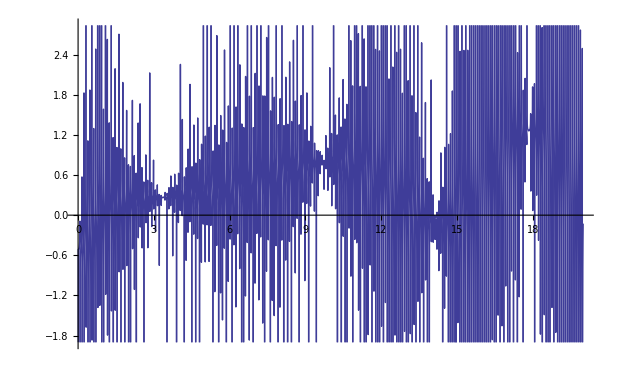

```mathematica
Plot[ Re@x4ay[1000000000000000000,N[1/3]+s I],{s,0,20}]
```

```mathematica
Zeta[N@ZetaZero@1-1/2+1/3]
```

-0.139457-0.0242355 ⅈ

```mathematica
FullSimplify[TrigToExp[1/2 (1+Coth[ArcTanh[1/2-(3 s)/2]-Log[n]/3+s Log[n]])]]
```

1/(1+(n^(2/3-2 s) (1+3 s))/(3 (-1+s)))

```mathematica
rr14a[n,t,s]
```

```mathematica
∑_(j=1)^n (j^(-s-t)/2+j^(s-t)/2)-Coth[ArcTanh[s/(-1+t)]+s Log[n]] ∑_(j=1)^n (-1/2 j^(-s-t)+j^(s-t)/2)
```

-1/2 Coth[ArcTanh[s/(-1+t)]+s Log[n]] (HarmonicNumber[n,-s+t]-HarmonicNumber[n,s+t])+1/2 (HarmonicNumber[n,-s+t]+HarmonicNumber[n,s+t])

```mathematica
TrigToExp[j^-t Sinh[s Log[j]]]
```

-1/2 j^(-s-t)+j^(s-t)/2

```mathematica
-1/2 Coth[ArcTanh[s/(-1+t)]+s Log[n]] (HarmonicNumber[n,-s+t])+1/2 (HarmonicNumber[n,-s+t])
```

1/2 HarmonicNumber[n,-s+t]-1/2 Coth[ArcTanh[s/(-1+t)]+s Log[n]] HarmonicNumber[n,-s+t]

```mathematica
-1/2 Coth[ArcTanh[s/(-1+t)]+s Log[n]] (HarmonicNumber[n,-s+t])+1/2 (HarmonicNumber[n,-s+t])/.s->-s+t
```

```mathematica
FullSimplify[1/2 HarmonicNumber[n,s]-1/2 Coth[ArcTanh[(-s+t)/(-1+t)]+(-s+t) Log[n]] HarmonicNumber[n,s]/.s->a+b I/.t->a]
```

1/2 (1-ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]]) HarmonicNumber[n,a+ⅈ b]

```mathematica
FullSimplify[(-1/2 Coth[ArcTanh[s/(-1+t)]+s Log[n]] (-HarmonicNumber[n,s+t])+1/2 (HarmonicNumber[n,s+t])/.s->-s+t)/.s->a+b I/.t->a]
```

1/2 (1+ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]]) HarmonicNumber[n,a-ⅈ b]

```mathematica
rr[n_,a_,b_]:=1/2 HarmonicNumber[n,a+ⅈ b]-1/2 ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]] HarmonicNumber[n,a+ⅈ b]
rrt[n_,a_,b_]:=rr[n,a,b]+rr[n,-a,b]
rrx[n_,a_,b_]:=(1- ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]])/2 HarmonicNumber[n,a+ⅈ b]
rrxa[n_,a_,b_]:=(1-I Cot[ArcTan[b/(-1+a)]+b Log[n]])/2 HarmonicNumber[n,a+ⅈ b]
rr2[n_,a_,b_]:=1/(1+((1-a+ⅈ b) n^(-2 ⅈ b))/(-1+a+ⅈ b))HarmonicNumber[n,a+ⅈ b]
rr3[n_,s_]:=(1-n^(Conjugate[s]-s)(Conjugate[s]-1)/(s-1))^-1HarmonicNumber[n,s]
rr3x[n_,s_]:=HarmonicNumber[n,s]
rr3y[n_,s_]:=(1-n^(Conjugate[s]-s)(Conjugate[s]-1)/(s-1))^-1
rr3z[n_,s_]:=(1-n^(Conjugate[s]-s)(Conjugate[s]-1)/(s-1))^-1 HarmonicNumber[n,s]
rr4[n_,s_]:=(1-(n^Conjugate[s](Conjugate[s]-1))/(n^s(s-1)))^-1 HarmonicNumber[n,s]
rr5[n_,s_]:=n^s(s-1)/(n^s(s-1)-n^Conjugate[s](Conjugate[s]-1) )HarmonicNumber[n,s]
```

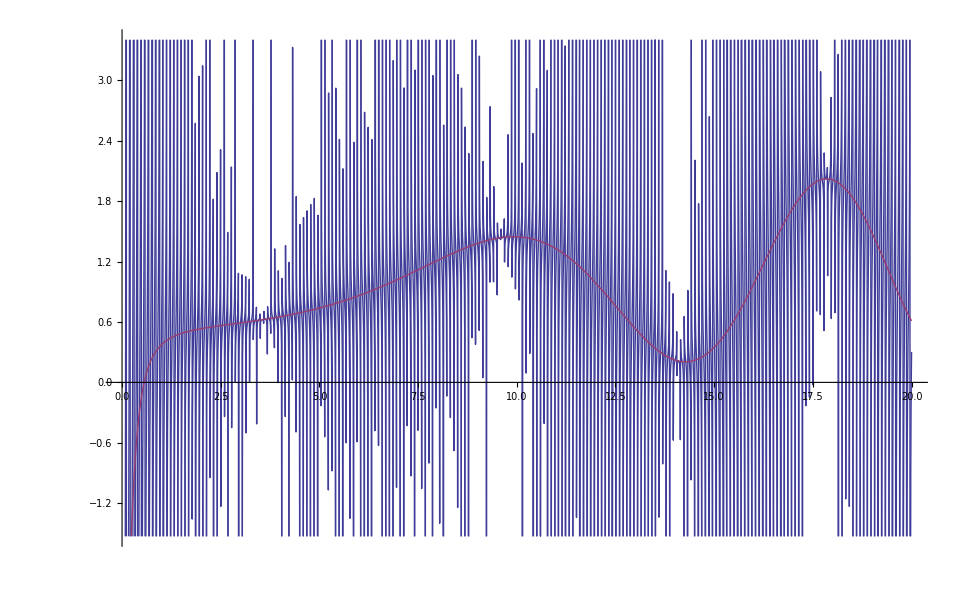

```mathematica
Plot[{2Re@rr3[1000000000000000,.8+s I],Re@Zeta[.8+s I]},{s,0,20}]
```

```mathematica
Zeta[.5+I]
```

0.143936-0.7221 ⅈ

```mathematica
FullSimplify[TrigToExp[(1- ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]])/2]]
```

1/(1+((1-a+ⅈ b) n^(-2 ⅈ b))/(-1+a+ⅈ b))

```mathematica
FullSimplify[1/(1+((1-a+ⅈ b) n^(-2 ⅈ b))/(-1+a+ⅈ b))]
```

1/(1+((1-a+ⅈ b) n^(-2 ⅈ b))/(-1+a+ⅈ b))

```mathematica
FullSimplify[(1-ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]])/2]
```

-1/2 ⅈ (ⅈ+Cot[ArcTan[b/(-1+a)]+b Log[n]])

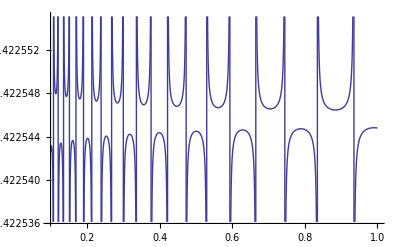

```mathematica
Plot[Re[rr2[n,.5,27.6701822178]],{n,10000000000,100000000000}]
```

```mathematica
Zeta[N@ZetaZero@1-.5+.2]/2
```

-0.132436-0.0246687 ⅈ

```mathematica
ps[n_,s_,t_]:=(1/n)Sum[N[ Re[rr2[j,s,t]]],{j,1,n}]
```

```mathematica
ps[100000,.2,N@Im@ZetaZero@1]
```

-0.0952945

```mathematica
(1+n^(-2 ⅈ b)(1-(a-ⅈ b))/(-1+a+ⅈ b))^-1/.a->.7/.b->.3/.n->20
```

0.5-4.39332 ⅈ

```mathematica
(1+n^(-(s-Conjugate[s]))(1-Conjugate[s])/(-1+s))^-1/.s->.7+.3I/.n->20
```

0.5-4.39332 ⅈ

```mathematica
(1-n^(Conjugate[s]-s)(Conjugate[s]-1)/(s-1))^-1/.s->.7+.3I/.n->20
```

0.5-4.39332 ⅈ

```mathematica
Conjugate[s]
```

Conjugate[s]

```mathematica
n^(-2 ⅈ b)/.a->.7/.b->.3/.n->20
```

-0.224708-0.974426 ⅈ

```mathematica
n^(-(s-Conjugate[s]))/.s->.7+.3I/.n->20
```

-0.224708-0.974426 ⅈ

```mathematica
(1-I Cot[ArcTan[b/(-1+a)]+b Log[n]])/2
```

```mathematica
1/2 (1-ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]])/.a->1/2/.b->14.4/.n->30
```

0.5-1.52274 ⅈ

```mathematica
1/2 (1-Tan[ArcTan[(a-1)/b]+b Log[n]])/.a->1/2/.b->14.4/.n->30
```

2.47589

```mathematica
FullSimplify[(1-(n^Conjugate[s](Conjugate[s]-1))/(n^s(s-1)))^-1]
```

1/(1-(n^(-2 ⅈ Im[s]) (-1+Conjugate[s]))/(-1+s))

```mathematica
(n^(-2 ⅈ Im[s]) (-1+Conjugate[s]))/(-1+s)/.s->N@ZetaZero@1
```

(-0.997501+0.0706593 ⅈ) n^(0.-28.2695 ⅈ)

```mathematica
(-1+Conjugate[s])/(-1+s)/.s->N@ZetaZero@1
```

-0.997501+0.0706593 ⅈ

```mathematica
(s-t I)/(s+ t I)/.s->.5
```

(0.5-ⅈ t)/(0.5+ⅈ t)

```mathematica
1/2 HarmonicNumber[n,s]-1/2 Coth[ArcTanh[(-s+t)/(-1+t)]+(-s+t) Log[n]] HarmonicNumber[n,s]/.s->Re[v]+Im[v]/.t->Re[v]
```

1/2 HarmonicNumber[n,Im[v]+Re[v]]+1/2 Coth[ArcTanh[Im[v]/(-1+Re[v])]+Im[v] Log[n]] HarmonicNumber[n,Im[v]+Re[v]]

```mathematica
1/2 HarmonicNumber[n,Im[v]+Re[v]]+1/2 Coth[ArcTanh[Im[v]/(-1+Re[v])]+Im[v] Log[n]] HarmonicNumber[n,Im[v]+Re[v]]/.v->s
```

```mathematica
(1+ Coth[ArcTanh[Im[s]/(-1+Re[s])]+Im[s] Log[n]]) HarmonicNumber[n,s]
```

```mathematica
FullSimplify[rr3y[n,.5 + t I]]
```

1/(1+(n^(-2 ⅈ Re[t]) (0.5+(0.+1. ⅈ) Conjugate[t]))/(-0.5+(0.+1. ⅈ) t))

```mathematica
1/(1+((1-a+ⅈ b) n^(-2 ⅈ b))/(-1+a+ⅈ b))HarmonicNumber[n,a+ⅈ b]/.a->s/.b->t
```

HarmonicNumber[n,s+ⅈ t]/(1+(n^(-2 ⅈ t) (1-s+ⅈ t))/(-1+s+ⅈ t))

```mathematica
1/(1+(n^(-2 ⅈ t) (1-s+ⅈ t))/(-1+s+ⅈ t))Sum[ 1 / j^(s+I t),{j,1,n}]
```

```mathematica
ExpToTrig[1/(1+(n^(-2 ⅈ t) (1-s+ⅈ t))/(-1+s+ⅈ t)) 1 / j^(s+I t)]
```

```mathematica
1/2 HarmonicNumber[n,s]-1/2 Coth[ArcTanh[(-s+t)/(-1+t)]+(-s+t) Log[n]] HarmonicNumber[n,s]/.s->a+b I/.t->b I
```

1/2 HarmonicNumber[n,a+ⅈ b]+1/2 Coth[ArcTanh[a/(-1+ⅈ b)]+a Log[n]] HarmonicNumber[n,a+ⅈ b]

```mathematica
rri[n_,a_,b_]:=1/2 HarmonicNumber[n,a+ⅈ b]+1/2 Coth[ArcTanh[a/(-1+ⅈ b)]+a Log[n]] HarmonicNumber[n,a+ⅈ b]
rrti[n_,a_,b_]:=rri[n,a,b]+rri[n,-a,b]
```

```mathematica
rrti[10000000,.5,N@Im@ZetaZero@1]
```

-0.0000107589+1.06315×10^-6 ⅈ

```mathematica
Zeta[.5]
```

-1.46035

```mathematica
rr14a[n_,m_,d_]:=Sum[j^-m  Cosh[d Log[j]],{j,1,n}]-Coth[ArcTanh[d/(-1+m)]+d Log[n]]Sum[j^-m  Sinh[d Log[j]],{j,1,n}]
rr14[n_,s_,t_]:=rr14a[n,(s+t)/2,(s-t)/2]
```

```mathematica
rr14[100000,N@ZetaZero@1-.3+10I,N@ZetaZero@1+.1]
```

0.0655803-0.00824799 ⅈ

```mathematica
Zeta[N@ZetaZero@1+.1]
```

0.0753346+0.0113729 ⅈ

```mathematica
rr4a[n_,m_,d_]:= ((1-(m-d))n^(m-d) HarmonicNumber[n,(m-d)]-(1-(m+d))n^(m+d) HarmonicNumber[n,(m+d)])/((1-(m-d))n^(m-d) -(1-(m+d))n^(m+d) )
rr4[n_,s_,t_]:=rr4a[n,(s+t)/2,(s-t)/2]
```

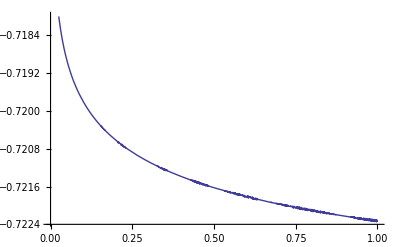

```mathematica
Plot[Im@rr4[n,.5+12I,.5+12I+.000001I],{n,1,10000000000}]
```

```mathematica
N@Zeta[.5+12I]
```

1.01594-0.745112 ⅈ

```mathematica
rr[n_,a_,b_]:=1/2 HarmonicNumber[n,a+ⅈ b]-1/2 ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]] HarmonicNumber[n,a+ⅈ b]
rrt[n_,a_,b_]:=rr[n,a,b]+rr[n,a,-b]
```

```mathematica
rrt[10000,.6,N@Im@ZetaZero@1]
```

-0.00650021+0. ⅈ

```mathematica
FullSimplify[(-1/2 Coth[ArcTanh[s/(-1+t)]+s Log[n]] (HarmonicNumber[n,-s+t]-HarmonicNumber[n,s+t])+1/2 (HarmonicNumber[n,-s+t]+HarmonicNumber[n,s+t])/.s->-s+t)/.s->a+b I/.t->a]
```

1/2 (HarmonicNumber[n,a-ⅈ b]+ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]] (HarmonicNumber[n,a-ⅈ b]-HarmonicNumber[n,a+ⅈ b])+HarmonicNumber[n,a+ⅈ b])

```mathematica
-1/2 ⅈ Cot[ArcTan[b/(-1+a)]+b Log[n]] (-HarmonicNumber[n,a-ⅈ b]+HarmonicNumber[n,a+ⅈ b])+1/2 (HarmonicNumber[n,a-ⅈ b]+HarmonicNumber[n,a+ⅈ b])/.n->10000000000000000/.a->.5/.b->3
```

0.60384+0. ⅈ

```mathematica
Zeta[.5+3I]
```

0.532737-0.0788965 ⅈ

```mathematica
1/2 Coth[ArcTanh[a/(-1+ⅈ b)]+a Log[n]] (-HarmonicNumber[n,-a+ⅈ b]+HarmonicNumber[n,a+ⅈ b])+1/2 (HarmonicNumber[n,-a+ⅈ b]+HarmonicNumber[n,a+ⅈ b])/.n->10000000000/.a->.6/.b->3
```

0.5-0.25 ⅈ

```mathematica
Zeta[.6+3I]
```

0.551963-0.0859178 ⅈ

```mathematica
Limit[ArcTanh[(-a-ⅈ b+c)/(-1+c)],c->1]
```

$Aborted

```mathematica
1/2 (HarmonicNumber[n,a]+ⅈ Cot[ArcTan[b/(-1+a+ⅈ b)]+b Log[n]] (HarmonicNumber[n,a]-HarmonicNumber[n,a+2 ⅈ b])+HarmonicNumber[n,a+2 ⅈ b])/.n->10000000000000/.a->.6/.b->3
```

0.753813+0.169326 ⅈ

```mathematica
Zeta[.6+6I]
```

0.845771+0.32451 ⅈ